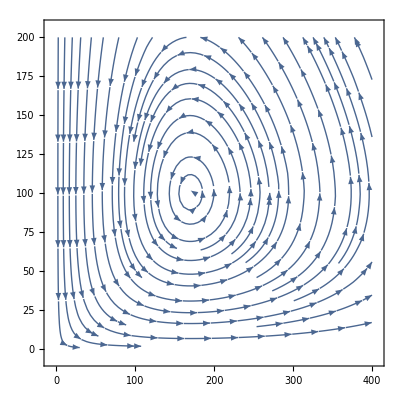

```mathematica
alpha = 100; gamma = 170;StreamPlot[{r*(alpha-s),s*(r-gamma)},{r,0,400},{s,0,200}]
```

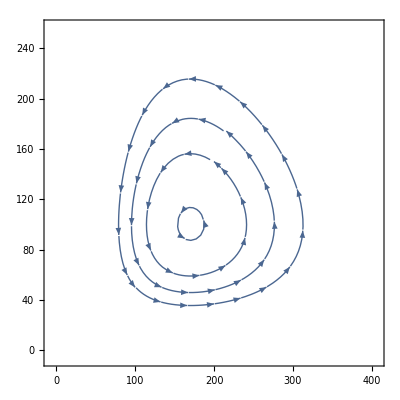

```mathematica
plot3 = StreamPlot[{r*(alpha-s),s*(r-gamma)},{r,0,400},{s,0,250},StreamPoints->{{100,50},{160,90},{200,150},{0,0}}]
```

```mathematica
wolfPop = {21,38,62,82,71,118,130,148,174,172,118,138,170,125,95,98,99,82,95,102}
```

{21,38,62,82,71,118,130,148,174,172,118,138,170,125,95,98,99,82,95,102}

```mathematica
wolfPop[[1]]
```

21

```mathematica
elkBisonPop = {20000,17900,16000,14400,12750,12700,15400,14450,13000,10200,9900,11300,10300,8550,8250,9350,8200,7500,7600,7500}
```

{20000,17900,16000,14400,12750,12700,15400,14450,13000,10200,9900,11300,10300,8550,8250,9350,8200,7500,7600,7500}

```mathematica
pts = Table[{wolfPop[[i]],elkBisonPop[[i]]},{i,1,Length[elkBisonPop]}]
```

{{21,20000},{38,17900},{62,16000},{82,14400},{71,12750},{118,12700},{130,15400},{148,14450},{174,13000},{172,10200},{118,9900},{138,11300},{170,10300},{125,8550},{95,8250},{98,9350},{99,8200},{82,7500},{95,7600},{102,7500}}

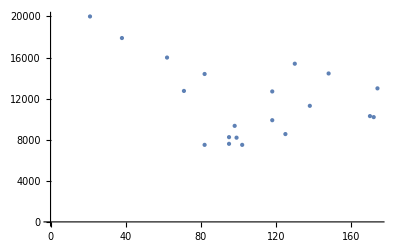

```mathematica
popPlot = ListPlot[pts,PlotStyle->PointSize[Large]]
```

```mathematica
ptsNew = Table[{wolfPop[[i]]/10,elkBisonPop[[i]]/1000},{i,1,Length[elkBisonPop]}];
```

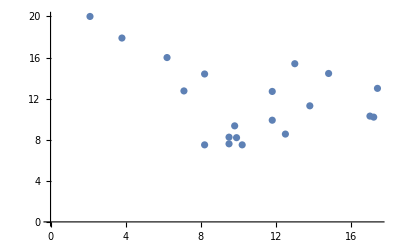

```mathematica
popPlotNew = ListPlot[ptsNew]
```

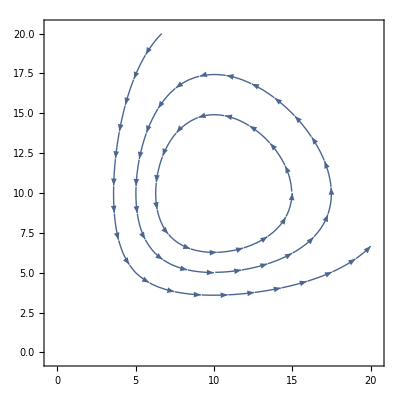

```mathematica
AA = 10; DD = 10;
plot3 = StreamPlot[{r*(AA-s),s*(r-DD)},{r,0,20},{s,0,20},StreamPoints->{{5,5},{10,5},{15,10}}]
```

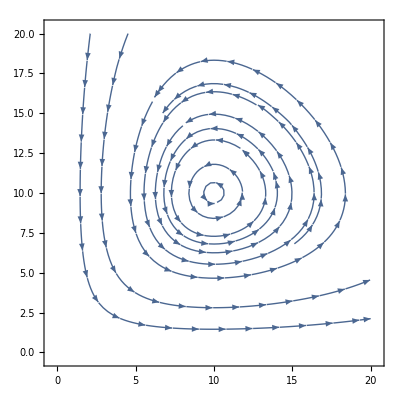

```mathematica
plot3 = StreamPlot[{r*(AA-s),s*(r-DD)},{r,0,20},{s,0,20},StreamPoints->ptsNew]
```

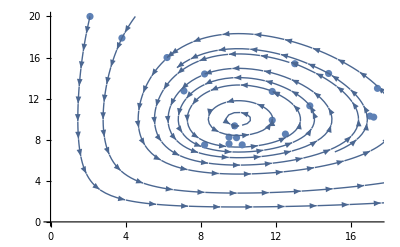

```mathematica
Show[popPlotNew,plot3]
```